```mathematica
ThreeDiagonalMethod[A_,B_,C_,F_]:=Module[{newB=Table[0,{i,1,Length[B]}],newC=Table[0,{i,1,Length[C]}],newF=Table[0,{i,1,Length[F]}],X=Table[0,{i,1,Length[B]}],α},
newB[[1]]=B[[1]];
newF[[1]]=F[[1]];
Do[
newB[[i]]=B[[i]]-A[[i]]/newB[[i-1]] C[[i-1]];
newF[[i]]=F[[i]]-A[[i]]/newB[[i-1]] newF[[i-1]];
,{i,2,Length[B]}
];
X[[-1]]=newF[[-1]]/newB[[-1]];
Do[
X[[i]]=(newF[[i]]-C[[i]]X[[i+1]])/newB[[i]];
,{i,Length[B]-1,1,-1}
];
Return[X];

]
```

```mathematica
Δx=0.1; Δy=0.1;
ε=10^-1;
```

## , ,

### Начальные условия

```mathematica
l1=2; l2=2;
f[x_,y_]:=0;
```

### Граничные условия

```mathematica
(*uΓ[x_,0]:=√(2x);
uΓ[0,y_]:=√y;
uΓ[x_,l2]:=√(x+√(x^2+4));
uΓ[l1,y_]:=√(1+√(1+y^2));*)
uΓ[x_,0]:=0;
uΓ[0,y_]:=5y(1+y^2);
uΓ[x_,l2]:=-30;
uΓ[l1,y_]:=-15 y^2/2;
```

## Решение “в лоб”

#### Сетка

#### Решение

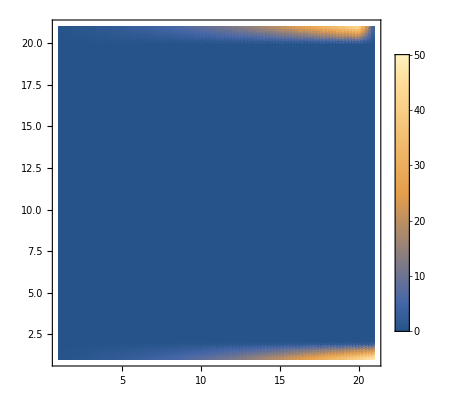

130

```mathematica
t=Δx^2/Δy^2;
φ=Table[f[i Δx,j Δy],{i,1,l1/Δx+1},{j,1,l2/Δy+1}];
Clear[u];
Do[
u[0,x,y]:=0;
, {x,2,l1/Δx}, {y,2,l2/Δy}];

u[k_,x_,1]:=uΓ[(x-1)Δx, 0];
u[k_,1,y_]:=uΓ[0,(y-1)Δy];
u[k_,x_,Round[l2/Δx+1]]:=uΓ[(x-1)Δx, 0];
u[k_,Round[l1/Δy+1],y_]:=uΓ[0,(y-1)Δy];

ListDensityPlot[Table[u[0,x,y],{x,1,l1/Δx+1},{y,1,l2/Δy+1}],PlotLegends->Automatic,InterpolationOrder->1]
kmax=1000.;
ProgressIndicator[Dynamic[k/kmax]]
For[k=0,k<kmax,k++,

eqs=Flatten[
Table[
u[k+1,x,y]==1/(2+2t)(u[k+1,x+1,y]+u[k,x-1,y]+t(u[k+1,x,y+1]+u[k,x,y-1]))-Δx^2/(2+2t)φ[[x,y]]
, {x,2,l1/Δx}, {y,2,l2/Δy}
]
];
vars=Flatten[Table[
u[k+1,x,y], {x,2,l1/Δx}, {y,2,l2/Δy}
]];
sol = NSolve[eqs, vars];
Do[
u[k+1,x,y]=First[u[k+1,x,y]/.sol];
, {x,1,l1/Δx+1}, {y,1,l2/Δy+1}
];
If[Norm[Table[u[k+1,x,y]-u[k,x,y], {x,1,l1/Δx+1}, {y,1,l2/Δy+1}]]<=ε,Break[]
]
];
Print[k];
```

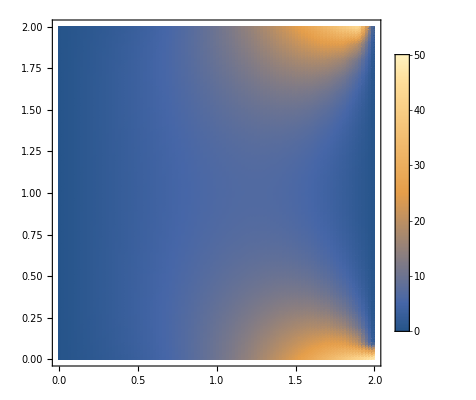

```mathematica
NumericSolution=Table[u[k,x,y],{x,1,l1/Δx+1},{y,1,l2/Δy+1}];
ListDensityPlot[NumericSolution,DataRange->{{0,l1}, {0,l2}},PlotLegends->Automatic,PlotRange->All,InterpolationOrder->1]
```

#### Решение

```mathematica
t=Δx^2/Δy^2;
φ=Table[f[i Δx,j Δy],{i,1,l1/Δx+1},{j,1,l2/Δy+1}];
iters={};

kmax=1000.;
ProgressIndicator[Dynamic[k/kmax]]
Do[
Clear[u];
Do[
u[0,x,y]:=0;
, {x,2,l1/Δx}, {y,2,l2/Δy}];

u[k_,x_,1]:=uΓ[(x-1)Δx, 0];
u[k_,1,y_]:=uΓ[0,(y-1)Δy];
u[k_,x_,Round[l2/Δx+1]]:=uΓ[(x-1)Δx, 0];
u[k_,Round[l1/Δy+1],y_]:=uΓ[0,(y-1)Δy];
For[k=0,k<kmax,k++,

eqs=Flatten[
Table[
u[k+1,x,y]==u[k,x,y]+ω(1/(2+2t)(u[k+1,x+1,y]+u[k,x-1,y]+t(u[k+1,x,y+1]+u[k,x,y-1]))-Δx^2/(2+2t)φ[[x,y]]-u[k,x,y])
, {x,2,l1/Δx}, {y,2,l2/Δy}
]
];
vars=Flatten[Table[
u[k+1,x,y], {x,2,l1/Δx}, {y,2,l2/Δy}
]];
sol = NSolve[eqs, vars];
Do[
u[k+1,x,y]=First[u[k+1,x,y]/.sol];
, {x,1,l1/Δx+1}, {y,1,l2/Δy+1}
];
If[Norm[Table[u[k+1,x,y]-u[k,x,y], {x,1,l1/Δx+1}, {y,1,l2/Δy+1}]]<=ε,Break[]]
];
AppendTo[iters,{ω,k}];
NumericSolution=Table[u[k,x,y],{x,1,l1/Δx+1},{y,1,l2/Δy+1}];

,{ω,0.1,1.9,0.1}];
```

InterpolatingFunction::dmval: Input value {0.0000408571} lies outside the range of data in the interpolating function. Extrapolation will be used.

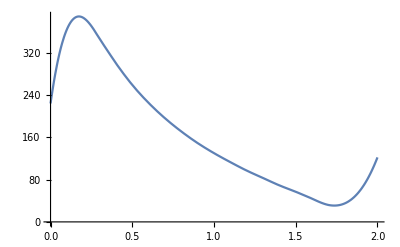

```mathematica
Plot[Interpolation[iters][x],{x,0,2}]
```

```mathematica
ω=1.7;
toch={};
Do[
ε=10^-t;
Clear[u];
Do[
u[0,x,y]:=0
,{x,2,l1/Δx}, {y,2,l2/Δy}
];

u[k_,x_,1]:=uΓ[(x-1)Δx, 0];
u[k_,1,y_]:=uΓ[0,(y-1)Δy];
u[k_,x_,Round[l2/Δx+1]]:=uΓ[(x-1)Δx, 0];
u[k_,Round[l1/Δy+1],y_]:=uΓ[0,(y-1)Δy];
For[k=0,k<kmax,k++,

eqs=Flatten[
Table[
u[k+1,x,y]==u[k,x,y]+ω(1/(2+2t)(u[k+1,x+1,y]+u[k,x-1,y]+t(u[k+1,x,y+1]+u[k,x,y-1]))-Δx^2/(2+2t)φ[[x,y]]-u[k,x,y])
, {x,2,l1/Δx}, {y,2,l2/Δy}
]
];
vars=Flatten[Table[
u[k+1,x,y], {x,2,l1/Δx}, {y,2,l2/Δy}
]];
sol = NSolve[eqs, vars];
Do[
u[k+1,x,y]=First[u[k+1,x,y]/.sol];
, {x,1,l1/Δx+1}, {y,1,l2/Δy+1}
];
If[Norm[Table[u[k+1,x,y]-u[k,x,y], {x,1,l1/Δx+1}, {y,1,l2/Δy+1}]]<=ε,Break[]]
];
AppendTo[toch,{ε,k}];
,{t,1,15}]
```

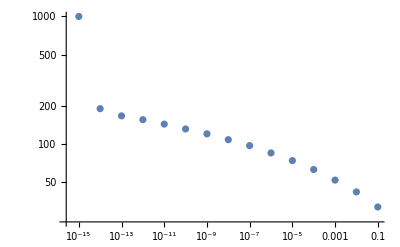

```mathematica
ListLogLogPlot[toch]
```